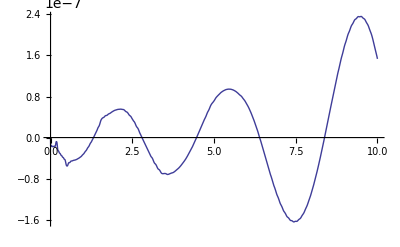

```mathematica
ysol=NDSolveValue[{y''[x]+1.5^2*y[x]==0,y[0]==0.5,y'[0]==1},y,{x,0,10}];
Plot[ysol[x]-5/6*Cos[(3 x)/2-ArcTan[4/3]],{x,0,10}]
```